# Orbital Elements in Plane Space

## Graphics and Computations along two Keplerian Orbits

```mathematica
ClearAll["Global`*"]
CartesianToKepler3D[r_List,u_List,t_,μ_:1]:=Module[
{
c,h,a,e,i,Ω,cosΩ,sinΩ,ω,cosωf,sinωf,M,cosE,sinE,EE,f,cosf,sinf,n,angle,T,τ
},
(* υπολογίζουμε την ενέργεια και την στροφορμή *)
c=1/2 Norm[u]^2-μ/Norm[r];
h=Cross[r,u];
(* διακόπτουμε τη ροή αν η ενέργεια βγει θετική - μας ενδιαφέρουν μόνο οι κλειστές τροχιές *)
If[c>0,Return[Style["Θετική ενέργεια --- Η τροχιά δεν είναι δέσμια.",{Red,Italic}]]];
(* υπολογίζουμε τα στοιχεία της τροχιάς *)
	(* μεγάλος ημιάξονας *)
a=-μ/(2c);
	(* εκκεντρότητα *)
e=√(1+(2c Norm[h]^2)/μ^2);
	(* κλίση της τροχιάς *)
i=ArcCos[h[[3]]/Norm[h]];
	(* μήκος του αναβιβάζοντος δεσμού *)
sinΩ=Sign[h[[3]]] h[[1]]/(Norm[h]Sin[i]);
cosΩ=-Sign[h[[3]]] h[[2]]/(Norm[h]Sin[i]);
Ω=Mod[#,2π]&[ArcTan[cosΩ,sinΩ]];
	(* Ε *)
cosE=(a-Norm[r])/(a e);
sinE=(r.u)/(e √(μ a));
EE=Mod[#,2π]&[ArcTan[cosE,sinE]];
	(* n *)
n=μ^(1/2)a^(-3/2);
	(* μέση ανωμαλία   M=E-e sinE *)
M=EE-e sinE;
	(* αληθής ανωμαλία f *)
cosf=(cosE-e)/(1-e cosE);
sinf=(√(1-e^2)sinE)/(1-e cosE);
f=Mod[#,2π]&[ArcTan[cosf,sinf]];
	(* γωνία περικέντρου ω *)
cosωf=(r[[1]] cosΩ+r[[2]]sinΩ)/Norm[r];
sinωf=r[[3]]/(Norm[r] Sin[i]);
ω=Mod[#,2π]&[ArcTan[cosωf,sinωf]-f];
	(* περίοδος *)
T=2π √(a^3/μ);
	(* τ *)
τ=t-M/n;

(* επιστρέφουμε τα αποτελέσματα *)
Association["a"->a,"e"->e,"i"->i,"Ω"->Ω,"ω"->ω,"M"->M,"τ"->τ,"T"->T,"n"->n]
]

KeplerToCartesian3D[a_,e_,i_,Ω_,ω_,M_]:=Module[
{
μ=1,
xTr,yTr,uxTr,uyTr,r,
P1,P2,P3,p,
EE,n,
temp
},
(* E από την εξίσωση του Kepler *)
EE=Last@Last@Quiet[FindRoot[M==temp-e Sin[temp],{temp,M}]];
(* θέση και ταχύτητα στο επίπεδο της τραχιάς *)
xTr=a(Cos[EE]-e);
yTr=a √(1-e^2)Sin[EE];
(* ακτίνα στο επίπεδο της τροχιάς *)
r=√(xTr^2+yTr^2);
(* μέση κίνηση n *)
n=μ^(1/2)a^(-3/2);
(* ταχύτητες πάνω στο επίπεδο της τροχιάς *)
uxTr=-(n a^2)/r Sin[EE];
uyTr=(n a^2)/r √(1-e^2)Cos[EE];
(* πίνακες στροφής: επίπεδο της κίνησης -> 3D *)
P1={{Cos[ω],-Sin[ω],0},{Sin[ω],Cos[ω],0},{0,0,1}};
P2={{1,0,0},{0,Cos[i],-Sin[i]},{0,Sin[i],Cos[i]}};
P3={{Cos[Ω],-Sin[Ω],0},{Sin[Ω],Cos[Ω],0},{0,0,1}};
p=P3.P2.P1;

(* αποτελέσματα: θέση & ταχύτητα στο χώρο *)
{p.{xTr,yTr,0},p.{uxTr,uyTr,0}}

]

DrawOrbit3D[T_,τ_,n_,a_,e_,i_,Ω_,ω_,colour_]:=Module[
{
nPoints=100,Ms,pts,xs,ys,xMin,xMax,yMin,yMax,plot
},
(* η M για χρόνο μίας περιόδου *)
Ms=Table[n(t-τ),{t,0,T,T/nPoints}];
(* τα σημεία της τροχιάς στον χρόνο μίας περιόδου *)
pts=Map[First,
Map[KeplerToCartesian3D[a,e,i,Ω,ω,#]&,Ms]
];
(* σχεδιασμός της τροχιάς *)
plot=ListPlot3D[pts,
Mesh->None,
PlotStyle->{colour,Opacity[0.5]}
];
xs=pts[[All,1]];
xMax=Max[xs];
xMin=Min[xs];
ys=pts[[All,2]];
yMax=Max[ys];
yMin=Min[ys];
<|"plot"->plot,"xMin"->xMin,"xMax"->xMax,"yMin"->yMin,"yMax"->yMax|>
]

MutualInclination[i1_,i2_,Ω1_,Ω2_]:=ArcCos[Cos[i1]Cos[i2]+Sin[i1]Sin[i2]Cos[Ω1-Ω2]];

ruPlots[T_,τ_,n_,a_,e_,i_,Ω_,ω_,tmin_,tmax_,nPoints_:100]:=Module[
{
Ms,data,ts,rs,us,rPlot,uPlot
},
(* υπολογισμος των M πάνω σε διακριτές χρονικές τιμές στο διάστημα που μας ενδιαφέρει *)
Ms=Table[{t,n(t-τ)},{t,tmin,tmax,T/nPoints}];
ts=Ms[[All,1]];
(* υπολογισμός της θέσης και της ταχύτητας για κάθε Μ *)
data=Map[KeplerToCartesian3D[a,e,i,Ω,ω,#]&,Ms[[All,2]]];
rs=Map[Norm[#]&,data[[All,1]]];
us=Map[Norm[#]&,data[[All,2]]];
(* διάγραμμα ακτίνας-χρόνου *)
rPlot=ListPlot[Transpose[{ts,rs}],Joined->True,PlotStyle->Black,PlotRange->All,AxesLabel->{"t","r"},PlotLabel->"r(t)"];
(* διάγραμμα ταχύτητας-χρόνου *)
uPlot=ListPlot[Transpose[{ts,us}],Joined->True,PlotStyle->Black,PlotRange->All,AxesLabel->{"t","u"},PlotLabel->"u(t)"];
<|"rPlot"->rPlot,"uPlot"->uPlot|>
]

OrbitalDistance[T1_,T2_,n1_,n2_,τ1_,τ2_,a1_,a2_,e1_,e2_,i1_,i2_,Ω1_,Ω2_,ω1_,ω2_,tmin_,tmax_,nPoints_:100]:=Module[
{
ts,Ms1,Ms2,rs1,rs2,ds,pts
},
(* δημιουργία των διακριτών χρονικών στιγμών που μας ενδιαφέρουν *)
ts=Table[t,{t,tmin,tmax,Max[T1,T2]/nPoints}];
(* υπολογισμός των Μ για τις τροχιές, για τους παραπάνω χρόνους *)
Ms1=Map[n1(#-τ1)&,ts];
Ms2=Map[n2(#-τ2)&,ts];
(* υπολογισμός της θέσης του κάθε σώματος στις παραπάνω στιγμές, μέσω της Μ *)
rs1=Map[KeplerToCartesian3D[a1,e1,i1,Ω1,ω1,#]&,Ms1][[All,1]];
rs2=Map[KeplerToCartesian3D[a2,e2,i2,Ω2,ω2,#]&,Ms2][[All,1]];
(* υπολογισμός της απόστασης μεταξύ των σωμάτων την κάθε στιγμή *)
ds=Map[Norm[Evaluate@(#[[1]]-#[[2]])]&,Transpose[{rs1,rs2}]];
(* διάγραμμα απόστασης-χρόνου *)
pts=Transpose[{ts,ds}];
ListPlot[pts,Joined->True,PlotStyle->Black,PlotRange->All,PlotLabel->"Orbital Distance",AxesLabel->{"t","d"},Epilog->{Blue,PointSize[0.005],Point[pts]}]
]

OrbitalDistanceD[T1_,T2_,n1_,n2_,τ1_,τ2_,a1_,a2_,e1_,e2_,i1_,i2_,Ω1_,Ω2_,ω1_,ω2_,tmin_,tmax_]:=Module[
{
ts,tCurrent=tmin,M1,M2,r1,r2,d,ds,
step,stepMin,stepMax,stepMod=0.25,
ttt,ddd,res,dOld,dNew,pts
},
stepMin=Min[T1,T2]/2000;
stepMax=Min[T1,T2]/20;
step=(stepMin+stepMax)/2;

res=Reap[
While[tCurrent≤tmax,
(* προσθήκη του χρόνου στη λίστα *)
Sow[tCurrent,ttt];
(* υπολογισμός της απόστασης για την παραπάνω στιγμή και προσθήκη της σε λίστα *)
M1=n1(tCurrent-τ1);
M2=n2(tCurrent-τ2);
r1=KeplerToCartesian3D[a1,e1,i1,Ω1,ω1,M1][[1]];
r2=KeplerToCartesian3D[a2,e2,i2,Ω2,ω2,M2][[1]];
d=Norm[r2-r1];
Sow[d,ddd];
(* αποθήκευση των δύο τελευταίων τιμών της απόστασης *)
If[tCurrent==tmin,dOld=d,dOld==dNew];
dNew=d;
(* υπολογισμός του νέου βήματος *)
If[dNew≤dOld,
If[step>stepMin,step=(1-stepMod)step],
If[step<stepMax,step=(1+stepMod)step]
];
(* αύξηση του χρόνου *)
tCurrent=tCurrent+step;
]];
ts=res[[2,1]];
ds=res[[2,2]];
pts=Transpose[{ts,ds}];
ListPlot[pts,Joined->True,PlotStyle->Black,PlotRange->All,PlotLabel->"Orbital Distance",AxesLabel->{"t","d"},PlotRange->All,Epilog->{Blue,PointSize[0.005],Point[pts]}]
]
```

-Graphics3D-

mutual inclination: 0.318336

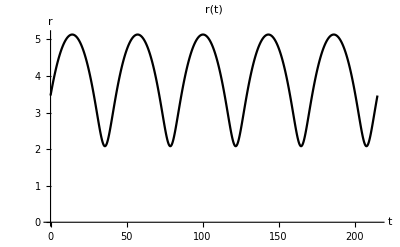
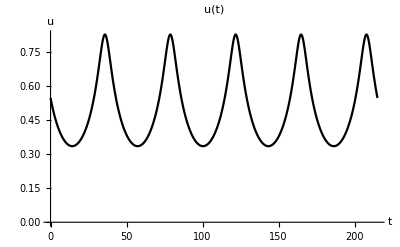
<|rPlot→-Graphics-,uPlot→-Graphics-|>

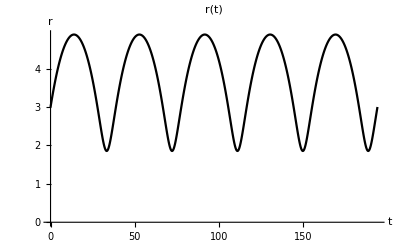
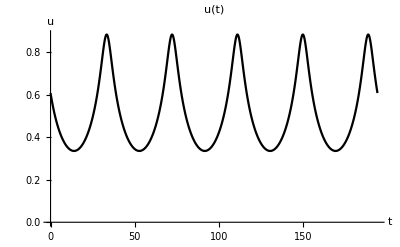
<|rPlot→-Graphics-,uPlot→-Graphics-|>

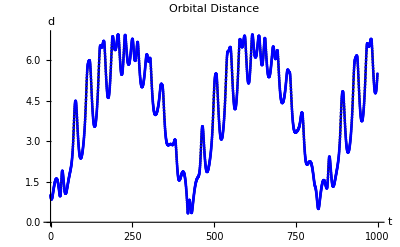
{3.53125,-Graphics-}

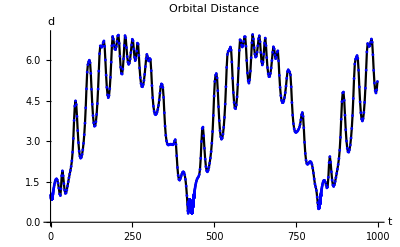
{3.04688,-Graphics-}

```mathematica
res1=CartesianToKepler3D[{2,2,2},{-0.2,0.5,0.1},0];
orbit1=DrawOrbit3D[res1["T"],res1["τ"],res1["n"],res1["a"],res1["e"],res1["i"],res1["Ω"],res1["ω"],Yellow];
res2=CartesianToKepler3D[{2,1,2},{0,0.6,0.1},0];
orbit2=DrawOrbit3D[res2["T"],res2["τ"],res2["n"],res2["a"],res2["e"],res2["i"],res2["Ω"],res2["ω"],Blue];
center=Graphics3D[{Green,Opacity[0.5],Sphere[{0,0,0},1]}];
zPlane=Plot3D[0,{x,Min[{orbit1["xMin"],orbit2["xMin"]}]-1,Max[{orbit1["xMax"],orbit2["xMax"]}]+1},{y,Min[{orbit1["yMin"],orbit2["yMin"]}]-1,Max[{orbit1["yMax"],orbit2["yMax"]}]+1},
Mesh->None,
PlotStyle->{Gray,Opacity[0.5]}
];

Show[{center,zPlane,orbit1["plot"],orbit2["plot"]},
AxesOrigin->{0,0,0},
Axes->True,
ImageSize->Large,
Boxed->False,
PlotRange->All
]
StringForm["mutual inclination: ``",MutualInclination[res1["i"],res2["i"],res1["Ω"],res2["Ω"]]]
ruPlots[res1["T"],res1["τ"],res1["n"],res1["a"],res1["e"],res1["i"],res1["Ω"],res1["ω"],0,5res1["T"],1000]
ruPlots[res2["T"],res2["τ"],res2["n"],res2["a"],res2["e"],res2["i"],res2["Ω"],res2["ω"],0,5res2["T"],1000]
Timing[OrbitalDistance[res1["T"],res2["T"],res1["n"],res2["n"],res1["τ"],res2["τ"],res1["a"],res2["a"],res1["e"],res2["e"],res1["i"],res2["i"],res1["Ω"],res2["Ω"],res1["ω"],res2["ω"],0,1000]]
Timing[OrbitalDistanceD[res1["T"],res2["T"],res1["n"],res2["n"],res1["τ"],res2["τ"],res1["a"],res2["a"],res1["e"],res2["e"],res1["i"],res2["i"],res1["Ω"],res2["Ω"],res1["ω"],res2["ω"],0,1000]]
```